```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
noise=Import["ansatz_noise.csv"];
```

```mathematica
nnoise=Import["ansatz_nonoise.csv"];
```

```mathematica
x=noise[[2;;,1]];
y=nnoise[[2;;,1]];
```

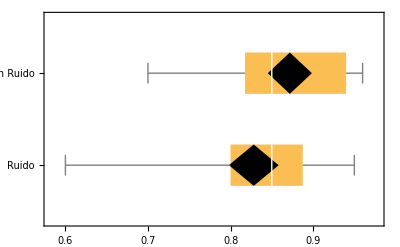

```mathematica
graf=BoxWhiskerChart[{x,y},{"Diamond",{"MeanDiamond",1,Black}},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```

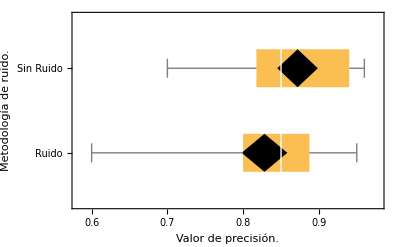

```mathematica
Show[graf,FrameLabel->{{RawBoxes[RowBox[{"Metodología"," ","de"," ",RowBox[{"ruido","."}]}]],None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],HoldForm[Distribución de la ejecución VQC Ansatz]}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
With[
{α=0.05,x=noise[[2;;,1]],
y=nnoise[[2;;,1]]},
KolmogorovSmirnovTest[x,y,"TestDataTable", SignificanceLevel->α]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.259259 | 0.166355

```mathematica
0.
```

```mathematica
ZTest[{x,y},1,0,"ShortTestConclusion",SignificanceLevel->0.05]
```

ZTest::nortst: At least one of the p-values in {0.00328951,0.000712009}, resulting from a test for normality, is below 0.025. The tests in {Z} require that the data is normally distributed.

Do not reject

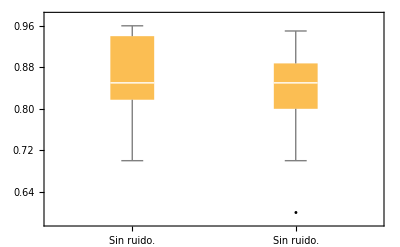

```mathematica
BoxWhiskerChart[Transpose/@{nnoise[[2;;,;;1]],noise[[2;;,;;1]]},"Outliers",ChartLabels->{"Sin ruido.","Ruido de Pauli"}]
```

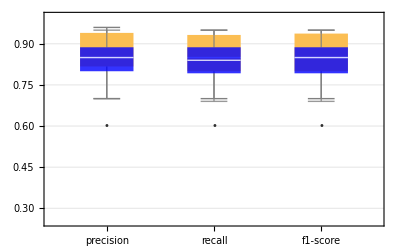

| Statistic | P-Value
Kolmogorov-Smirnov | 0.259259 | 0.155

```mathematica
Show[{{BoxWhiskerChart[nnoise[[2;;,;;]]ᵀ,"Outliers", ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed",PlotRange->{0.25,1},ChartLabels->{"No Noise"}]},{BoxWhiskerChart[noise[[2;;,;;]]ᵀ,"Outliers",  ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed",PlotRange->{0.25,1},ChartStyle->{Opacity[0.8],{Blue,Blue,Blue},ChartLabels->{"Noise"}}]}}]
```

```mathematica
AndersonDarlingTest[%]
```

0.0659758

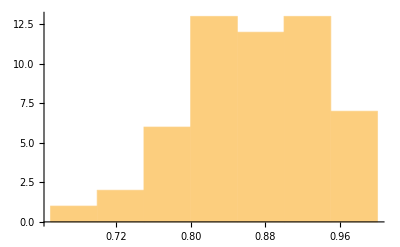

```mathematica
Join[nnoise[[2;;,1]],nnoise[[2;;,1]]-RandomReal[]/10]//Histogram
```

```mathematica
SignedRankTest[{nnoise[[2;;,1]],noise[[2;;,1]]}]
```

0.0194609

```mathematica
MardiaSkewnessTest[nnoise[[2;;,1]]]
```

0.289557

```mathematica
PearsonChiSquareTest[nnoise[[2;;,1]],noise[[2;;,1]]]
```

0.852472

```mathematica
With[
{x=nnoise[[2;;,2]],
y=noise[[2;;,2]]},
KolmogorovSmirnovTest[x,y,"PValueTable"]]
```

| P-Value
Kolmogorov-Smirnov | 0.209751

```mathematica
With[
{x=nnoise[[2;;,3]],
y=noise[[2;;,3]]},
KolmogorovSmirnovTest[x,y,"PValueTable"]]
```

| P-Value
Kolmogorov-Smirnov | 0.297191

```mathematica
PairedHistogram[nnoise[[2;;,1]],noise[[2;;,1]],8, PlotTheme->"Detailed"]
```

-Graphics-

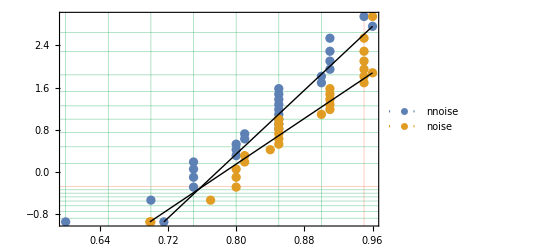

```mathematica
ProbabilityScalePlot[{noise[[2;;,1]],nnoise[[2;;,1]]},PlotLegends->{"nnoise","noise"}, GridLines->Automatic, GridLinesStyle->"Classic",PlotRange->Full]
```

```mathematica
Table[((2π-i)/(2π))*100//N,{i,0,1,0.1}]
```

{100.,98.4085,96.8169,95.2254,93.6338,92.0423,90.4507,88.8592,87.2676,85.6761,84.0845}

```mathematica
100-%
```

{0.,1.59155,3.1831,4.77465,6.3662,7.95775,9.5493,11.1408,12.7324,14.3239,15.9155}